```mathematica
SetDirectory["~/doc/research/first_order_singularities/paper"];
```

```mathematica
<<IsingScalingFunction`
```

```mathematica
data2={θ0->1.14841,θYL->0.989667,CYL->-0.172824,G[1]->-0.310183,G[2]->0.247454,g[0]->0.373691,g[1]->-0.0216363}
```

{θ0→1.14841,θYL→0.989667,CYL→-0.172824,G[1]→-0.310183,G[2]→0.247454,g[0]→0.373691,g[1]→-0.0216363}

```mathematica
prep2={θ0,θYL,ruleB[θ0,{g[0],g[1]}],ruleAL[θ0,{g[0],g[1]}],CYL,{G[1],G[2]},{g[0],g[1]}}/.data2
```

{1.14841,0.989667,5.08816,-0.0114291,-0.172824,{-0.310183,0.247454},{0.373691,-0.0216363}}

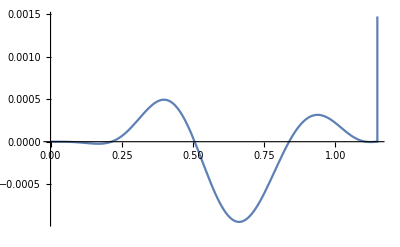

```mathematica
Plot[Evaluate@Last[(DScriptF0DηList@@prep2)[6,θ]],{θ,0,1.1483}]
```

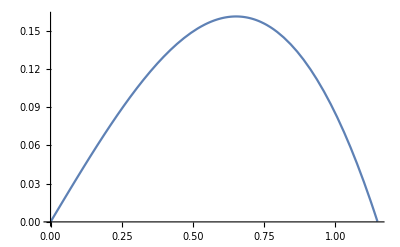

```mathematica
Plot[Evaluate[g[θ0,{g[0],g[1]}][θ]/.data2],{θ,0,1.148}]
```

```mathematica
ComplexPlot[(ScriptF@@Most@prep2)[θ],{θ,3}]
```

-Graphics-

```mathematica
(uf@@Most[prep2])[1,θ]
```

-0.172824 (-1.98276+(0.989667-ⅈ θ)^(5/6)+(0.989667+ⅈ θ)^(5/6))-0.310183 θ^2+0.247454 θ^4-0.00363798 (-1.84268+ⅇ^(-0.196535/(-1.14841-θ)) (-1.14841-θ) ExpIntegralEi[0.196535/(-1.14841-θ)])-0.00363798 (-1.84268+ⅇ^(-0.196535/(-1.14841+θ)) (-1.14841+θ) ExpIntegralEi[0.196535/(-1.14841+θ)])

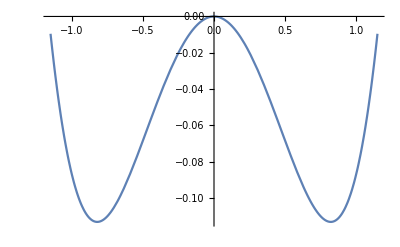

```mathematica
Plot[(uf@@Most[prep2])[1,θ],{θ,-1.148,1.148}]
```

```mathematica
test=DufDut[θ0,θYL,B,C0,CYL,{},{g[0]}][2][R,θ];
```

```mathematica
Series[test,{θ,0,0},Assumptions->{R>0,θ0>0,g[0]>1}]
```

(45-8 Log[θ^2 g[0]^2]+16 Log[R^(15/4) θ^2 g[0]^2])/(120 π)+O[θ]^1

```mathematica
8/60
```

2/15

```mathematica
16/120
```

2/15

```mathematica
D[96 B^2 θ0^3 θYL^(7/6) Log[θ^2 g[0]^2] θ^2,{θ,2}]
```

576 B^2 θ0^3 θYL^(7/6)+192 B^2 θ0^3 θYL^(7/6) Log[θ^2 g[0]^2]

```mathematica
Series[test,{θ,θ0,0},Assumptions->{R>0,θ0>0,g[0]>1}]
```

$Aborted

```mathematica
Series[(1-1/(g[θ0,{g[0]}][θ])^(2/Δ)),{θ,0,1},Assumptions->{θ>0}]
```

1+θ^(-2/Δ) (-g[0]^(-2/Δ)+O[θ]^2)

```mathematica
dat=Flatten[Table[{ut[R,θ],uh[θ0,{g[0],g[1]}][R,θ],-(DufDuh@@prep2)[1][R,θ]}/.data2,{R,0.05,2,0.05},{θ,-1.14841,1.14841,0.05}],1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPlot3D[dat]
```

-Graphics3D-

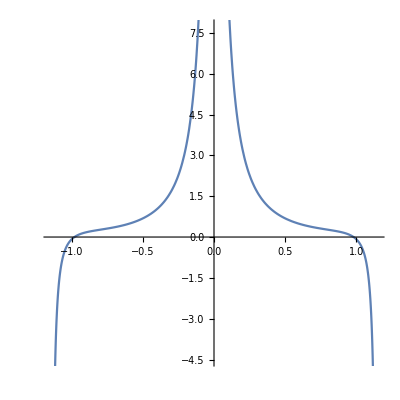

```mathematica
ParametricPlot[{θ,Evaluate[(DufDut@@prep2)[1][1,θ]]},{θ,-1.148,1.148},AspectRatio->1]
```

```mathematica
dGdξ
```

```mathematica
(dΦdηList@@prep2)[0,1]
```

{-1.19741+0. ⅈ}

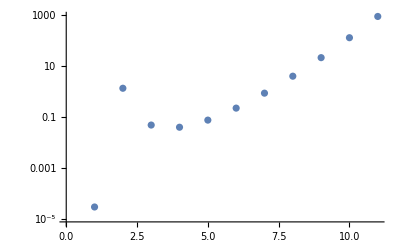

```mathematica
ListLogPlot[Abs[(DScriptFPlusMinusDξθ0List@@prep2)[10]]]
```

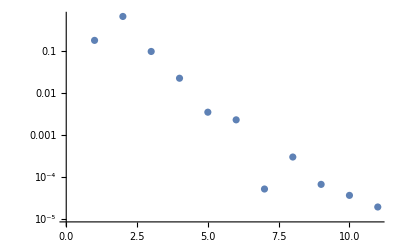

```mathematica
ListLogPlot[Abs[(DScriptF0DηList@@prep2)[10,0.5]]]
```

```mathematica
dza
```

```mathematica
Function[θ,Evaluate@h[θ0,{g1,g2}][θ]]
```

Function[θ,h[θ0,{g1,g2}][θ]]

```mathematica
DerivativeList[f_,x_,n_]:=Through[NestList[Derivative[1],f,n][x]]
EfficientDerivativeList[f_,x_,n_]:=Module[{xp},NestList[Function[g,D[g,xp]],f[xp],n]/.xp->x]
```

```mathematica
f[x_]:=Log[x^(1/2)] x^(3/7)Sin[x^(1/3)]
```

```mathematica
Timing[DerivativeList[f,x,10];]
```

{5.33547,Null}

```mathematica
data=Map[n↦First[Timing[DerivativeList[f,6,n]]],Range[8]]
efficientData=Map[n↦First[Timing[EfficientDerivativeList[f,6,n]]],Range[13]]
```

{0.000217,0.000525,0.001141,0.00335,0.009593,0.03427,0.141814,0.578457}

{0.000233,0.000344,0.000584,0.000931,0.001271,0.001725,0.002238,0.002929,0.003621,0.004433,0.005236,0.006274,0.007287}

```mathematica
Timing[Derivative[#][f][6]&/@Range[13];]
```

{0.006562,Null}

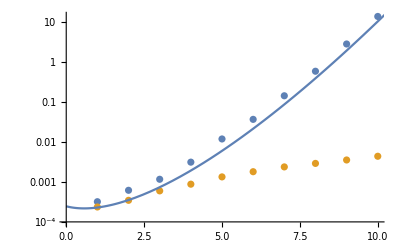

```mathematica
Show[
ListLogPlot[{data,efficientData}],
LogPlot[(4/5 x)!/4000,{x,0,12}]
]
```